```mathematica
SetDirectory["/home/meike/Documents/"];
Get["PlotTheme.m"]
$PlotTheme="Publication";
Needs["ErrorBarPlots`"];
SetDirectory[]; 
path="/home/meike/Documents/literature/conferences/Elisbon/day07/exercise2/run06/";
```

```mathematica
settings=Import[path<>"settings.dat"]
tmax=settings[[1,2]];
dt=settings[[2,2]];
Ngrid=settings[[3,2]];
tprint=settings[[4,2]];
```

{{tmax,1000},{dt,0.1},{N,100},{tprint,10},{lambda,0.1},{Pe,3.16228}}

```mathematica
tplus=IntegerPart[tprint/dt];
tmaxsteps=IntegerPart[tmax/dt];
gridt={};
mean={};
For[t = 0, t < tmaxsteps, t+=tplus, 
grid=Import[path<>"grid_t"<>ToString[t]<>".dat"];
AppendTo[gridt,grid];
AppendTo[mean,{t*dt,Mean[Flatten[grid]]}]
]
frame[t_]:=ListDensityPlot[gridt[[t]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic,ImageSize->800]
```

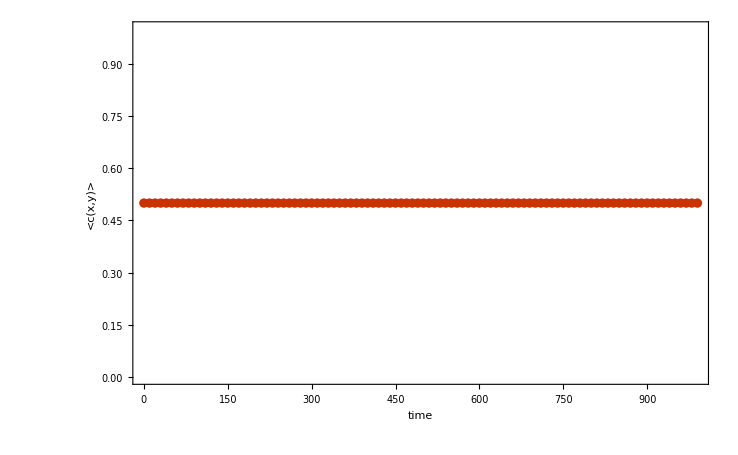

```mathematica
meanplot=ListPlot[mean,FrameLabel->{"time","<c(x,y)>"}]
```

```mathematica
Export["/home/meike/Dropbox/phd/figures/day7_ex2_mean.png",meanplot]
```

/home/meike/Dropbox/phd/figures/day7_ex2_mean.png

```mathematica
Manipulate[ListDensityPlot[gridt[[step]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic],{step,1,Length[gridt],1}];
```

ParallelTable::nopar1: ParallelTable[frame[t],{1,100,1}] cannot be parallelized; proceeding with sequential evaluation.

Table::itraw: Raw object 1 cannot be used as an iterator.

Table[frame[t],{1,100,1}]

```mathematica
frames=ParallelTable[frame[t],{t,1,Length[gridt],1}];
```

```mathematica
Export["/home/meike/day7_ex2_frames.avi",frames]
```

day7_ex2_frames.avi

```mathematica
ListPlot[mean]
```

-Graphics-

```mathematica
ew
```

```mathematica
ListPlot[mean]
```

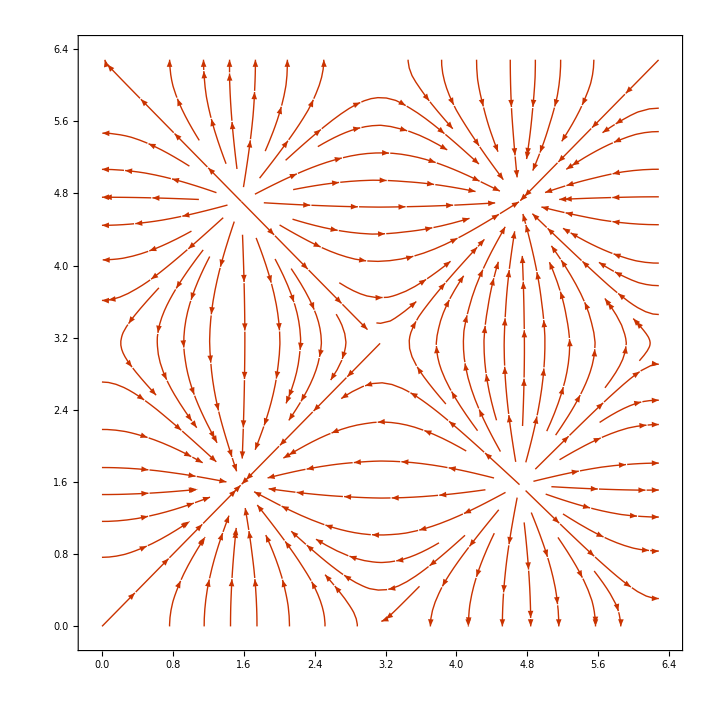

```mathematica
stream=StreamPlot[{0.5*Cos[x]*Sin[y],0.5*Sin[x]*Cos[y]},{x,0,2π},{y,0,2π}]
```

```mathematica
Export["/home/meike/Dropbox/phd/figures/day7_stream.png",stream]
```

/home/meike/Dropbox/phd/figures/day7_stream.png

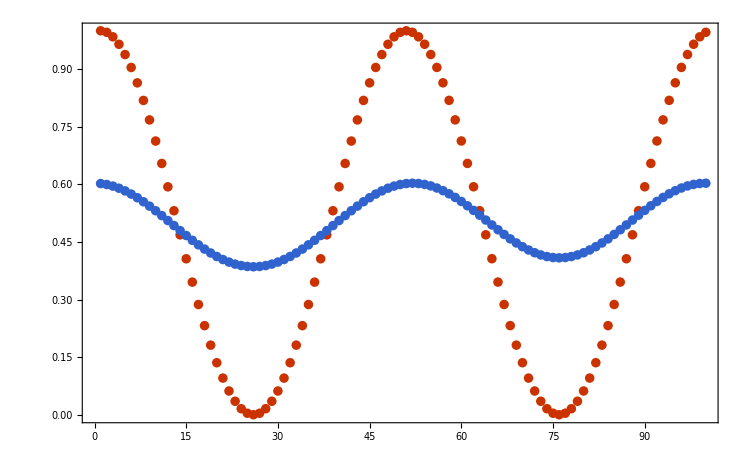

```mathematica
ListPlot[{gridt[[1,All,25]],gridt[[2,All,25]]}]
```

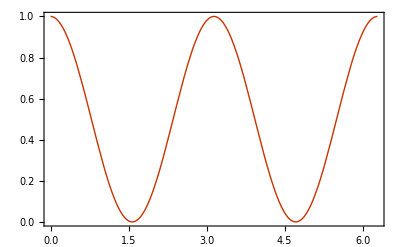

```mathematica
Plot[Cos[x]^2,{x,0,2π}]
```

```mathematica
Remove[t,c]
```

```mathematica
DSolve[{D[c[t,x,y],t]+0.5*Cos[x]*Sin[y]*D[c[t,x,y],x]+0.5*Sin[x]*Cos[y]*D[c[t,x,y],y]==D[c[t,x,y],x]+D[c[t,x,y],y],c[0,x,y]==Cos[x]^2},c[t,x,y],{t}]
```

{{c[t,x,y]→Cos[x]^2+(1.+0. ⅈ) ((0.+0. ⅈ)+(1.+0. ⅈ) c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x-1. y] c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,0,1)[K[1],x,y]+(1.+0. ⅈ) c^(0,1,0)[K[1],x,y]+(0.25+0. ⅈ) Sin[x-1. y] c^(0,1,0)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,1,0)[K[1],x,y])K[1]0t}}